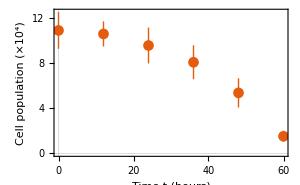

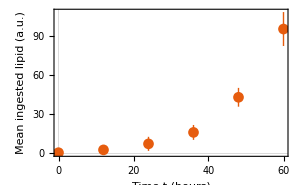

1266

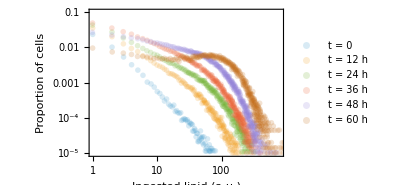

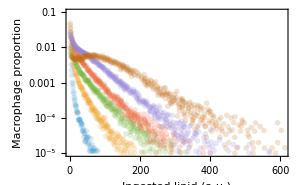

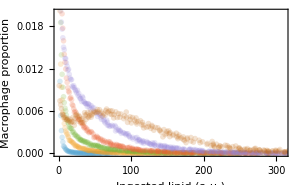

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

rawMdata={{0,Around[10.86,1.62]},{12,Around[10.55,1.11]},{24, Around[9.53,1.58]},{36,Around[8.05,1.50]},{48,Around[5.35,1.29]},{60,Around[1.52,0.49]}};
rawLdata={{0,Around[0.6153869553665652,0]},{12,Around[2.7692354303844904,0.8]},{24,Around[7.384619989338658,5.4]},{36,Around[16.153845956339673,5.7]},{48,Around[43.076922550239054,7.2]},{60,Around[95.38461715276893,13.0]}};

ListPlot[rawMdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Cell population (×10^4)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}]
ListPlot[rawLdata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}]

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.2;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid (a.u.)", "Proportion of cells"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid (a.u.)", "Proportion of cells"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,410},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid (a.u.)", "Proportion of cells"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid (a.u.)", "Proportion of cells"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
(* Log-likelihood function *)
ClearAll[completeloglikelihood];

completeloglikelihood[{η_?NumericQ,e_?NumericQ,μ_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodM,loglikelihoodm,outcome,λ,w},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ,afun_?NumericQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
(*etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)*)
(*alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)>*)*)
conv=Prepend[Take[ListConvolve[fvec,v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
η/μ*afun *(conv-v)+(betaBar-βvec)*v
];

imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t]],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η*A[t]), A[0]==0};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99||(M[t]<0.01&&t<55),"StopIntegration";outcome=1]},{u,M, A},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48,60}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,6}];

loglikelihoodm=Sum[1/Length[resamples[[j]]]*Sum[-Log[resamples[[j]][[i]][[2]]*(1-resamples[[j]][[i]][[2]])*(σm*Sqrt[12*(j-1)])*Sqrt[2 Pi]]-1/(2*(σm*Sqrt[12*(j-1)])^2)*(Log[resamples[[j]][[i]][[2]]/(1-resamples[[j]][[i]][[2]])]-Log[moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]]/(1-moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]])])^2,{i,1,Length[resamples[[j]]]}],{j,2,6}];


If[outcome==0&&Element[loglikelihoodM+loglikelihoodm,Reals],loglikelihoodM+loglikelihoodm,-10^(6)]
]

(* Plot function *)

completeplots[{η_?NumericQ,e_?NumericQ,μ_?NumericQ, cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,Loutput,modeldistributionplotloglinear,modeldistributionplotloglog,modelAplot},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ,afun_?NumericQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
(*etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)*)
(*alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)>*)*)
conv=Prepend[Take[ListConvolve[fvec,v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
η/μ*afun *(conv-v)+(betaBar-βvec)*v
];

imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t]],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η*A[t]), A[0]==0};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M, A},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),0.1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];

modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,61},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,60},PlotRange->{{-0.5,61},{-0.05,101}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean lipid content (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelAplot=Plot[{(A[t]/.sol[[1]])/(e+idx.(u[0]/. sol[[1]]))*(M[0]/.sol[[1]]),(e+idx.(u[t]/. sol[[1]]))*(M[t]/.sol[[1]])/(e+idx.(u[0]/. sol[[1]]))*(M[0]/.sol[[1]])},{t,0,60},PlotRange->{{-0.5,61},{-0.05,1.1}},PlotStyle->Automatic,ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Lipid content L (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];

Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot],modelAplot},{Show[distributionlinearplot,modeldistributionplot],Show[distributionloglinearplot,modeldistributionplotloglinear],Show[distributionloglogplot,modeldistributionplotloglog]}}]
]

priorfn[x_]:=PDF[UniformDistribution[{0,500}]][x]
priorη[x_]:=PDF[LogNormalDistribution[-1.354944,0.763522],x]

logposterior[{η_?NumericQ,enew_?NumericQ,μnew_?NumericQ, cv_?NumericQ,β0new_?NumericQ,β1new_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=Log[priorη[η]]+Log[priorfn[enew]]+Log[priorfn[μnew]]+Log[priorfn[cv]]+Log[priorfn[β0new]]+Log[priorfn[β1new]]+Log[priorfn[σM]]+Log[priorfn[σm]]+completeloglikelihood[{η,100*enew,100*μnew,cv,β0new/100,β1new/100,1,σM,σm}]
```

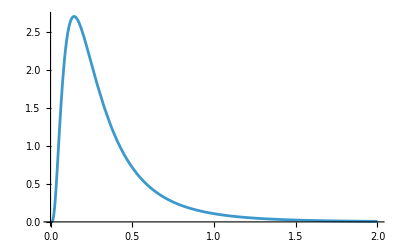

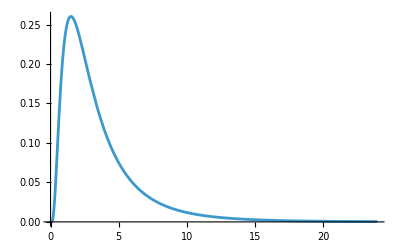

```mathematica
Plot[priorη[x],{x,0,2},PlotRange->All]
Plot[PDF[LogNormalDistribution[0.988431,0.763522],x],{x,0,24},PlotRange->{0,All}]
```

```mathematica
logposterior[{1/1.1648690761445004,0.45678485333129604,0.25125740370214716,2.0401195183578524,0.28305056061173944,0.12501594802739271,0.16585737490624927,0.08955628116339767}]
```

-322.199

```mathematica
(*MCMC functions*)
makePositiveDefinite[mat_?MatrixQ,tol_:1.*^-12]:=Module[{sym,evMin},sym=(mat+Transpose[mat])/2;
evMin=Min[Re[Eigenvalues[sym]]];
If[evMin>tol,sym,sym+(-evMin+tol) IdentityMatrix[Length[sym]]]];

Options[metropolisAdaptive]={AdaptDelay->20,Eps->1.*^-4,InitCov->Automatic,PrintEvery->20,(*Previously 1000*)TargetAcc->0.25,(*Previously 0.234*)AccWindow->1000,AccTol->0.02,Gamma0->1,(*Initial learning-rate numerator*)GammaAlpha->0.6,(*Exponent in gamma_t=Gamma0/t^GammaAlpha*)MinAdaptIters->20000,(*Minimum adaptation updates before stopping*)ConsecOK->10,(*Consecutive acceptable windows required to stop*)LambdaRange->{0.01,5.},(*Allowed lambda interval*)MaxAdaptIters->Infinity};



metropolisAdaptive[init_?VectorQ,nsamples_Integer?Positive,opts:OptionsPattern[]]/;AllTrue[init,NumericQ]:=Module[{dim=Length[init],s,chain,current=init,currentLogPost,proposalCov,proposalDist,prop,propLogPost,logA,u,accepted=0,i,empCov,baseCov,adaptDelay=OptionValue[AdaptDelay],eps=OptionValue[Eps],initCov=OptionValue[InitCov],printEvery=OptionValue[PrintEvery],target=OptionValue[TargetAcc],accWindow=OptionValue[AccWindow],accTol=OptionValue[AccTol],gamma0=OptionValue[Gamma0],gammaAlpha=OptionValue[GammaAlpha],minAdaptIters=OptionValue[MinAdaptIters],consecOK=OptionValue[ConsecOK],lambdaRange=OptionValue[LambdaRange],maxAdaptIters=OptionValue[MaxAdaptIters],lambda=1,adaptOn=True,adaptUpdates=0,acceptHistory,historyLen=0,historyPos=1,acceptedFlag,consecOKcount=0,finalProposalCov,globalAccRate=0.},
s=2.38^2/dim;
If[!IntegerQ[adaptDelay]||adaptDelay<1,Message[metropolisAdaptive::badDelay,adaptDelay];
adaptDelay=100];
If[accWindow<1,accWindow=1];
If[gamma0<=0,gamma0=0.02];
If[gammaAlpha<=0,gammaAlpha=0.6];
baseCov=Which[MatrixQ[initCov]&&Dimensions[initCov]==={dim,dim},initCov,initCov===Automatic,eps IdentityMatrix[dim],True,eps IdentityMatrix[dim]];
baseCov=makePositiveDefinite[baseCov,10^-12];
chain=ConstantArray[0.,{nsamples,dim}];
chain[[1]]=current;
currentLogPost=logposterior[current];
acceptHistory=ConstantArray[0,accWindow];(*Circular buffer of recent acceptances*)
historyLen=0;
historyPos=1;
finalProposalCov=s baseCov;
Monitor[Do[If[adaptOn&&i-1>=2&&i>adaptDelay+1,empCov=Covariance[Take[chain,i-1]];
If[!MatrixQ[empCov]||Dimensions[empCov]=!={dim,dim},empCov=baseCov];
proposalCov=makePositiveDefinite[lambda s (empCov+eps IdentityMatrix[dim]),10^-12];(*Adaptive proposal covariance*)finalProposalCov=proposalCov,proposalCov=finalProposalCov];
proposalDist=MultinormalDistribution[current,proposalCov];
prop=RandomVariate[proposalDist];

If[AnyTrue[prop,#<0&]||prop[[3]]<0.01,(*Reject proposals containing negative elements*)acceptedFlag=0,(*Otherwise evaluate the log posterior*)propLogPost=TimeConstrained[logposterior[prop],5,$TimedOut];
If[propLogPost===$TimedOut,acceptedFlag=0;
Print["TIMEOUT at iteration ",i," | prop = ",InputForm[prop]],logA=propLogPost-currentLogPost;
u=Log[RandomReal[]];
If[u<Min[0,logA],current=prop;
currentLogPost=propLogPost;
acceptedFlag=1;
accepted++,acceptedFlag=0]]];

chain[[i]]=current;
acceptHistory[[historyPos]]=acceptedFlag;
historyPos=If[historyPos==accWindow,1,historyPos+1];
historyLen=Min[historyLen+1,accWindow];
If[adaptOn&&i>adaptDelay+1,Module[{accWindowRate,gammaT},accWindowRate=N[Total[Take[acceptHistory,historyLen]]/historyLen];
adaptUpdates++;
If[adaptUpdates>maxAdaptIters,adaptOn=False,gammaT=gamma0/Max[1,adaptUpdates]^gammaAlpha;(*Diminishing adaptation rate*)lambda=lambda Exp[gammaT (accWindowRate-target)];
lambda=Clip[lambda,lambdaRange];
If[adaptUpdates>=minAdaptIters&&Abs[accWindowRate-target]<=accTol,consecOKcount++,consecOKcount=0];
If[consecOKcount>=consecOK,adaptOn=False                                               (*Stop after enough acceptable windows*)]]]];
If[IntegerQ[printEvery]&&printEvery>0&&Mod[i,printEvery]==0,Export["currentMCMC4.mx",chain]                              (*Periodic checkpoint*)],{i,2,nsamples}],Dynamic[Module[{winAcc,gAcc},winAcc=If[historyLen>0,N[Total[Take[acceptHistory,historyLen]]/historyLen],0.];
gAcc=If[i>1,N[accepted/(i-1)],0.];
Row[{"Iteration: ",If[ValueQ[i],i,1]," | Global acc: ",NumberForm[gAcc,{4,3}]," | Window acc(",historyLen,"): ",NumberForm[winAcc,{4,3}]," | adapting?: ",adaptOn," | lambda: ",NumberForm[lambda,{5,4}]}]]]];
<|"Chain"->chain,"AcceptanceRate"->N[accepted/(nsamples-1)],"FinalProposalCov"->finalProposalCov,"FinalLambda"->lambda,"AdaptStopped"->!adaptOn,"AdaptUpdates"->adaptUpdates|>]
```

```mathematica
(*--------------------Run MCMC sampler--------------------*)

SetDirectory[NotebookDirectory[]];

nSamples=100000;

proposalCov={{0.003593225432815464,-0.005249096754125093,0.00036816700649156843,0.0015146901147724157,-0.00020725419241822144,0.002416444640312266,-0.00033385387388891626,0.0008858577532047658},{-0.005249096754125093,0.03258530035993209,-0.0018855993788699042,-0.006800855359226922,-0.0006278881748109664,0.003564498280936377,-0.0019984948919465322,-0.0006312313461978958},{0.00036816700649156843,-0.0018855993788699042,0.011655530359908843,-0.029070451158439602,0.00004880668664530056,-0.0019880237603273642,-0.0001234615217068543,0.0013316251714169886},{0.0015146901147724157,-0.006800855359226922,-0.029070451158439602,0.17068398598351767,-0.00015551450194926683,0.0029988084621116093,0.0000340330734493713,0.0020620204960184302},{-0.00020725419241822144,-0.0006278881748109664,0.00004880668664530056,-0.00015551450194926683,0.0010096185846204366,-0.010246412322995552,0.0020492092646940616,-0.00010316098879564967},{0.002416444640312266,0.003564498280936377,-0.0019880237603273642,0.0029988084621116093,-0.010246412322995552,0.1241877596859549,-0.0186291235908323,0.0010060082055716865},{-0.00033385387388891626,-0.0019984948919465322,-0.0001234615217068543,0.0000340330734493713,0.0020492092646940616,-0.0186291235908323,0.009411335206905173,-0.00044685552759019757},{0.0008858577532047658,-0.0006312313461978958,0.0013316251714169886,0.0020620204960184302,-0.00010316098879564967,0.0010060082055716865,-0.00044685552759019757,0.0020699068243674726}};

dval=8;
sval=(2.38^2)/dval;
initCovToPass=proposalCov/sval;

f=1.0;
init=f*{η,e,μ,cv,β0,β1,σM,σm}/.{η->0.17847354970391763,e->0.864644471031164,μ->0.17610275774519996,cv->1.8493490281344782,β0->0.1507830844337915,β1->7.643744820259895,σM->0.15790599544729683,σm->0.09750442527799377};

res=metropolisAdaptive[init,nSamples,InitCov->initCovToPass,AdaptDelay->2nSamples (*to ensure no adaptation *)]//Quiet;
chain=res["Chain"];
acc=res["AcceptanceRate"];
Print["Acceptance rate: ",acc];
Print[res["FinalProposalCov"]];
Print[chain//Last];

Export["MCMC_etaprior_tdep_100k.mx",chain]
```

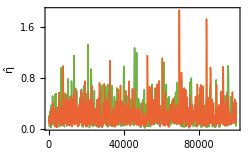
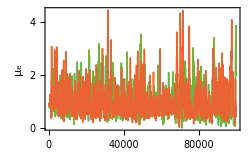
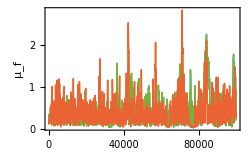
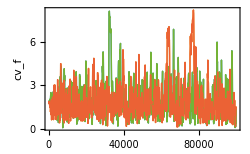
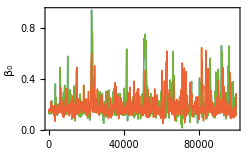
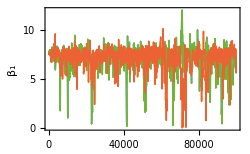
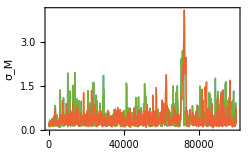
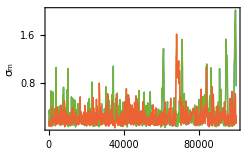

```mathematica
(*--------------------Load chains (example using samples of the subcellular model) --------------------*)
SetDirectory[NotebookDirectory[]];
chainFiles={"MCMC1_etaprior_tdep_100k.mx","MCMC2_etaprior_tdep_100k.mx","MCMC3_etaprior_tdep_100k.mx","MCMC4_etaprior_tdep_100k.mx"};

chains=Import/@chainFiles;

(*--------------------Settings--------------------*)
names={"chain1","chain2","chain3","chain4"};

(*--------------------Extract posteriors and parameter series--------------------*)
posteriorChains=Map[#[[1;;All;;1]]&,chains];

npar=8;
combinedSamplesList=Table[Map[#[[All,i]]&,posteriorChains],{i,1,npar}];

(*If chains have different lengths,truncate to the shortest so they align visually*)
minLen=Min[Length/@combinedSamplesList[[1]]];
Do[combinedSamplesList[[i]]=Map[Take[#,minLen]&,combinedSamplesList[[i]]],{i,1,npar}]

(*--------------------Trace plots (three chains on each plot)--------------------*)
ranges=Table[{0,All},{i,1,8}];
names={"η̂","μ_e","μ_f","cv_f","β_0","β_1","σ_M","σ_m"};

traceplots=Table[ListLinePlot[combinedSamplesList[[i]],PlotRange->ranges[[i]],PlotStyle->Thin,MaxPlotPoints->1000,Frame->True,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},FrameLabel->{"Iteration",names[[i]]},ImageSize->250],{i,1,npar}]
```

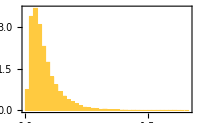
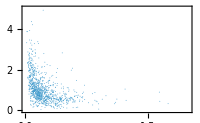
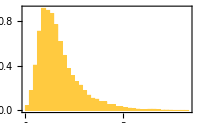
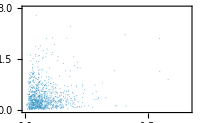
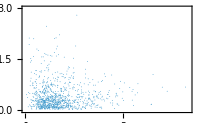
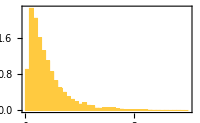
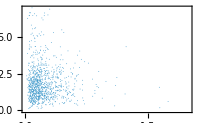
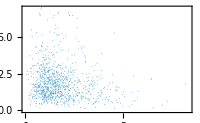
-Graphics-η̂ |  |  |  |  |  |  | 
-Graphics-μ_e | -Graphics- |  |  |  |  |  | 
-Graphics-μ_f | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics-cv_f | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics-β_0 | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics-β_1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics-σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics-η̂σ_m | -Graphics-μ_e | -Graphics-μ_f | -Graphics-cv_f | -Graphics-β_0 | -Graphics-β_1 | -Graphics-σ_M | -Graphics-σ_m

```mathematica
(* -------------Pair scatter+marginal histograms--------------*)

burnin=0;    
thin=1;              
posteriorChains=Map[#[[burnin+1;;All;;thin]]&,chains];

npar=8;
pooledSamples=Table[Join[Map[#[[burnin+1;;All;;thin]]&,combinedSamplesList[[i]]]//Flatten],{i,1,npar}];

vars=pooledSamples;
vars[[6]]=1/100*vars[[6]];
(*vars[[2]]=100*vars[[2]];
vars[[3]]=100*vars[[3]];
vars[[5]]=1/100*vars[[5]];
vars[[6]]=1/100*vars[[6]];*)

names={"η̂","μ_e","μ_f","cv_f","β_0","β_1","σ_M","σ_m"};
ranges={{0,2},{0,5},{0,3},{0,7},{0,1},{0,0.1},{0,2},{0,2}};

img=200;         (*image size for each cell*)
pt=0.003;        (*point size for scatter*)
bins=40;         (* histogram bin number *)

diag[i_]:=Histogram[vars[[i]],{ranges[[i]][[1]],ranges[[i]][[2]],(ranges[[i]][[2]]-ranges[[i]][[1]])/bins},"PDF",PlotRange->{ranges[[i]],All(*{0,All}*)},Frame->True,FrameTicks->Automatic,ImageSize->img,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},ImagePadding->{{30, 20}, {15, 15}}];
pair[i_,j_]:=ListPlot[Transpose[{vars[[j]],vars[[i]]}],PlotStyle->PointSize[pt],PlotRange->{ranges[[j]],ranges[[i]]},Frame->True,FrameTicks->Automatic,ImageSize->img,MaxPlotPoints->1000,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},ImagePadding->{{30, 20}, {15, 15}}];

grid=Table[Which[i==j,diag[i],i>j,pair[i,j],True,Nothing],{i,1,npar},{j,1,npar}];

addLabels[plot_,i_,j_]:=Module[{p=plot},If[i==Length[vars],p=Labeled[p,names[[j]],Bottom]];If[j==1,p=Labeled[p,names[[i]],Left]];p];

labeledGrid=MapIndexed[addLabels[#1,First[#2],Last[#2]]&,grid,{2}];

(*display*)
Grid[labeledGrid,Spacings->{1,1}]
```

```mathematica
quantiles=Table[Quantile[vars[[i]],{0.05,0.5,0.95}],{i,1,npar}];
quantileTable={{names[[1]],0.06,0.18,0.60},{names[[2]],32,88,233},{names[[3]],6,29,115},{names[[4]],0.59,1.66,4.27},{names[[5]],0.0011,0.0016,0.0039},{names[[6]],0.05,0.07,0.08},{names[[7]],0.15,0.32,1.15},{names[[8]],0.10,0.20,0.60}}(*Table[{names[[i]],NumberForm[quantiles[[i,1]],{Infinity,2}],NumberForm[quantiles[[i,2]],{Infinity,2}],NumberForm[quantiles[[i,3]],{Infinity,2}]},{i,1,npar}];*)
Grid[Prepend[quantileTable,{"Parameter","5% quantile", "Median","95% quantile"}],Frame->All,Alignment->Center,Spacings->{2,1}]
```

{{η̂,0.06,0.18,0.6},{μ_e,32,88,233},{μ_f,6,29,115},{cv_f,0.59,1.66,4.27},{β_0,0.0011,0.0016,0.0039},{β_1,0.05,0.07,0.08},{σ_M,0.15,0.32,1.15},{σ_m,0.1,0.2,0.6}}

Parameter | 5% quantile | Median | 95% quantile
η̂ | 0.06 | 0.18 | 0.6
μ_e | 32 | 88 | 233
μ_f | 6 | 29 | 115
cv_f | 0.59 | 1.66 | 4.27
β_0 | 0.0011 | 0.0016 | 0.0039
β_1 | 0.05 | 0.07 | 0.08
σ_M | 0.15 | 0.32 | 1.15
σ_m | 0.1 | 0.2 | 0.6

```mathematica
logposterior[{1/1.1648690761445004,0.45678485333129604,0.25125740370214716,2.0401195183578524,0.28305056061173944,0.12501594802739271,0.16585737490624927,0.08955628116339767}]
```

-3.8301

```mathematica
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}={1/1.1648690761445004,0.45678485333129604,0.25125740370214716,2.0401195183578524,0.28305056061173944,0.12501594802739271,0.16585737490624927,0.08955628116339767};
FindMaximum[{logposterior[{η,100*e,100*μ,cv,β0/100,β1/100,σM,σm}],0.01<e<2,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.01<β1<1,0.01<σM<0.5,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,σM,σm},logposterior[{η,100*e,100*μ,cv,β0/100,β1/100,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.858466,0.456785,0.251257,2.04012,0.283051,0.125016,0.165857,0.0895563},-352.349}

$Aborted

```mathematica
ClearAll[splitChains,averageRanks,rankNormalize,scalarRHat,rankSplitRHat,foldedRankSplitRHat,modernRHat];

(*Split each chain into first and second halves.If a chain has odd length,drop the last draw.*)
splitChains[chains_]:=Module[{n,half},
n=Min[Length/@chains];
half=Floor[n/2];
Join@@Table[{chains[[c,1;;half]],chains[[c,half+1;;2 half]]},{c,Length[chains]}]];

(*Average ranks,so ties receive their average rank*)
averageRanks[x_List]:=Module[{ord,sorted,groups,ranks},
ord=Ordering[x];
sorted=Sort[x];(*x[[ord]];*)
groups=Split[Range[Length[x]],sorted[[#1]]==sorted[[#2]]&];
ranks=ConstantArray[0.,Length[x]];
Do[ranks[[ord[[g]]]]=Mean[g],{g,groups}];
ranks];

(*Blom rank-normalization:z_i=InverseCDF[NormalDistribution[],(r_i-3/8)/(S+1/4)]*)
rankNormalize[x_List]:=Module[{s,r},
s=Length[x];
r=averageRanks[x];
InverseCDF[NormalDistribution[0,1],(r-3/8)/(s+1/4)]];

(*Ordinary split-Rhat formula for scalar split chains*)
scalarRHat[splitScalarChains_]:=Module[{m,n,chainMeans,chainVars,w,b,varPlus},
m=Length[splitScalarChains];
n=Length[First[splitScalarChains]];
chainMeans=Mean/@splitScalarChains;
chainVars=Variance/@splitScalarChains;
w=Mean[chainVars];
b=n Variance[chainMeans];
varPlus=((n-1)/n) w+(1/n) b;
Sqrt[varPlus/w]];

(*Rank-normalized split-Rhat for scalar chains*)
rankSplitRHat[scalarChains_]:=Module[{split,flat,z,dims},
split=splitChains[scalarChains];
dims=Length/@split;
flat=Flatten[split];
z=rankNormalize[flat];
scalarRHat[TakeList[z,dims]]];

(*Folded rank-normalized split-Rhat for scalar chains*)
foldedRankSplitRHat[scalarChains_]:=Module[{split,flat,med,folded,z,dims},
split=splitChains[scalarChains];
dims=Length/@split;
flat=Flatten[split];
med=Median[flat];
folded=Abs[flat-med];
z=rankNormalize[folded];
scalarRHat[TakeList[z,dims]]];

(*Modern Rhat for vector-valued chains.Returns coordinate-wise Rhat and the max.*)
modernRHat[chains_]:=Module[{d,scalarChainsByDim,rhatRank,rhatFolded,rhat},d=Length[chains[[1,1]]];
scalarChainsByDim=Table[chains[[All,All,k]],{k,d}];
rhatRank=rankSplitRHat/@scalarChainsByDim;
rhatFolded=foldedRankSplitRHat/@scalarChainsByDim;
rhat=MapThread[Max,{rhatRank,rhatFolded}];
<|"RankSplitRHat"->rhatRank,"FoldedRankSplitRHat"->rhatFolded,"RHat"->rhat,"MaxRHat"->Max[rhat]|>];
```

```mathematica
scalarRHat[chains]
```

{1.00001,1.00081,1.00013,1.00001,1.00229,1.00009,1.00167,1.00408}

```mathematica
(*Number of samples*)
n=Min[500000,Min[Length/@pooledSamples]];

(*Rows=samples,columns=parameters*)
samples=N@Transpose[(Take[#,n]&/@pooledSamples)];

(*Rank-transform columns*)
ranks=Transpose[Ordering[Ordering[#]]&/@Transpose[samples]];

(*Spearman correlation matrix*)
R=Correlation[ranks];

(*PRCC matrix*)
P=Inverse[R];

prccMatrix=N@Table[If[i==j,1.,-P[[i,j]]/Sqrt[P[[i,i]] P[[j,j]]]],{i,8},{j,8}];

(*------------------------------------------------------------*)(*Keep only lower-left triangle*)(*------------------------------------------------------------*)lowerPRCC=Table[If[i>=j,NumberForm[prccMatrix[[i,j]],{4,2}],""],{i,npar},{j,npar}];

MatrixForm[lowerPRCC,TableHeadings->{names,names}]
```

( | η̂ | μ_e | μ_f | cv_f | β_0 | β_1 | σ_M | σ_m
η̂ | 1.00 |  |  |  |  |  |  | 
μ_e | -0.61 | 1.00 |  |  |  |  |  | 
μ_f | -0.13 | -0.23 | 1.00 |  |  |  |  | 
cv_f | -0.17 | -0.27 | -0.85 | 1.00 |  |  |  | 
β_0 | -0.22 | -0.29 | -0.09 | -0.09 | 1.00 |  |  | 
β_1 | -0.19 | -0.22 | -0.11 | -0.12 | -0.89 | 1.00 |  | 
σ_M | 0.03 | 0.03 | 0.05 | 0.06 | -0.03 | -0.23 | 1.00 | 
σ_m | 0.04 | 0.04 | 0.24 | 0.11 | 0.01 | 0.03 | 0.04 | 1.00)

```mathematica
MatrixForm[lowerPRCC,TableHeadings->{names,names}]
```

( | η̂ | μ_e | μ_f | cv | β_0 | β_1 | σ_M | σ_m
η̂ | 1.00 |  |  |  |  |  |  | 
μ_e | -0.61 | 1.00 |  |  |  |  |  | 
μ_f | -0.13 | -0.23 | 1.00 |  |  |  |  | 
cv | -0.17 | -0.27 | -0.85 | 1.00 |  |  |  | 
β_0 | -0.22 | -0.29 | -0.09 | -0.09 | 1.00 |  |  | 
β_1 | -0.19 | -0.22 | -0.11 | -0.12 | -0.89 | 1.00 |  | 
σ_M | 0.03 | 0.03 | 0.05 | 0.06 | -0.03 | -0.23 | 1.00 | 
σ_m | 0.04 | 0.04 | 0.24 | 0.11 | 0.01 | 0.03 | 0.04 | 1.00)

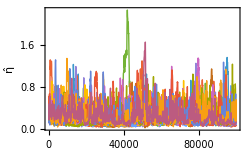
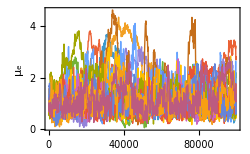
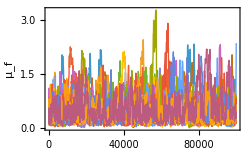
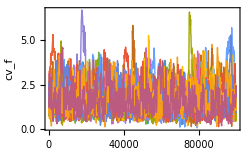
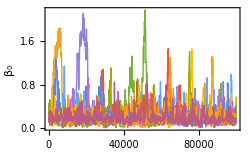
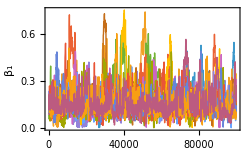
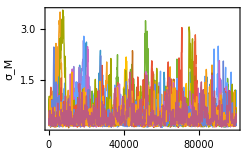
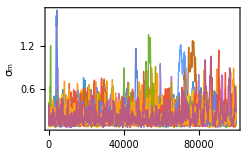

```mathematica
(*--------------------Load chains (example using samples of the subcellular model) --------------------*)
SetDirectory[NotebookDirectory[]];
chainFiles={"MCMC1_etaprior_ldep_100k.mx","MCMC2_etaprior_ldep_100k.mx","MCMC3_etaprior_ldep_100k.mx","MCMC4_etaprior_ldep_100k.mx","MCMC5_etaprior_ldep_100k.mx","MCMC6_etaprior_ldep_100k.mx","MCMC7_etaprior_ldep_100k.mx","MCMC8_etaprior_ldep_100k.mx","MCMC9_etaprior_ldep_100k.mx","MCMC10_etaprior_ldep_100k.mx","MCMC11_etaprior_ldep_100k.mx","MCMC12_etaprior_ldep_100k.mx","MCMC13_etaprior_ldep_100k.mx","MCMC14_etaprior_ldep_100k.mx"};

chains=Import/@chainFiles;

(*--------------------Settings--------------------*)
names={"chain1","chain2","chain3","chain4"};

(*--------------------Extract posteriors and parameter series--------------------*)
posteriorChains=Map[#[[1;;All;;1]]&,chains];

npar=8;
combinedSamplesList=Table[Map[#[[All,i]]&,posteriorChains],{i,1,npar}];

(*If chains have different lengths,truncate to the shortest so they align visually*)
minLen=Min[Length/@combinedSamplesList[[1]]];
Do[combinedSamplesList[[i]]=Map[Take[#,minLen]&,combinedSamplesList[[i]]],{i,1,npar}]

(*--------------------Trace plots (three chains on each plot)--------------------*)
ranges=Table[{0,All},{i,1,8}];
names={"η̂","μ_e","μ_f","cv_f","β_0","β_1","σ_M","σ_m"};

traceplots=Table[ListLinePlot[combinedSamplesList[[i]],PlotRange->ranges[[i]],PlotStyle->Thin,MaxPlotPoints->1000,Frame->True,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},FrameLabel->{"Iteration",names[[i]]},ImageSize->250],{i,1,npar}]
```

```mathematica
scalarRHat[chains]
```

{1.00987,1.03595,1.00888,1.00835,1.01133,1.00785,1.00769,1.00416}

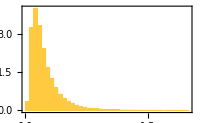
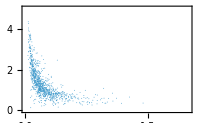
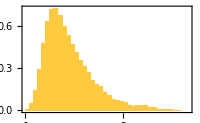
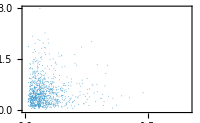
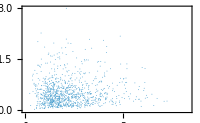
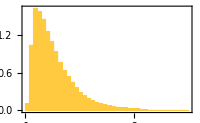
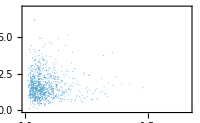
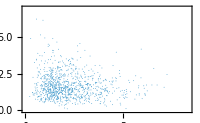
-Graphics-η̂ |  |  |  |  |  |  | 
-Graphics-μ_e | -Graphics- |  |  |  |  |  | 
-Graphics-μ_f | -Graphics- | -Graphics- |  |  |  |  | 
-Graphics-cv_f | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics-β_0 | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics-β_1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics-σ_M | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics-η̂σ_m | -Graphics-μ_e | -Graphics-μ_f | -Graphics-cv_f | -Graphics-β_0 | -Graphics-β_1 | -Graphics-σ_M | -Graphics-σ_m

```mathematica
(* -------------Pair scatter+marginal histograms--------------*)

burnin=0;    
thin=1;              
posteriorChains=Map[#[[burnin+1;;All;;thin]]&,chains];

npar=8;
pooledSamples=Table[Join[Map[#[[burnin+1;;All;;thin]]&,combinedSamplesList[[i]]]//Flatten],{i,1,npar}];

vars=pooledSamples;
(*vars[[6]]=1/100*vars[[6]];*)
(*vars[[2]]=100*vars[[2]];
vars[[3]]=100*vars[[3]];
vars[[5]]=1/100*vars[[5]];
vars[[6]]=1/100*vars[[6]];*)

names={"η̂","μ_e","μ_f","cv_f","β_0","β_1","σ_M","σ_m"};
ranges={{0,2},{0,5},{0,3},{0,7},{0,1},{0,1},{0,2},{0,2}};

img=200;         (*image size for each cell*)
pt=0.003;        (*point size for scatter*)
bins=40;         (* histogram bin number *)

diag[i_]:=Histogram[vars[[i]],{ranges[[i]][[1]],ranges[[i]][[2]],(ranges[[i]][[2]]-ranges[[i]][[1]])/bins},"PDF",PlotRange->{ranges[[i]],All(*{0,All}*)},Frame->True,FrameTicks->Automatic,ImageSize->img,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},ImagePadding->{{30, 20}, {15, 15}}];
pair[i_,j_]:=ListPlot[Transpose[{vars[[j]],vars[[i]]}],PlotStyle->PointSize[pt],PlotRange->{ranges[[j]],ranges[[i]]},Frame->True,FrameTicks->Automatic,ImageSize->img,MaxPlotPoints->1000,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},ImagePadding->{{30, 20}, {15, 15}}];

grid=Table[Which[i==j,diag[i],i>j,pair[i,j],True,Nothing],{i,1,npar},{j,1,npar}];

addLabels[plot_,i_,j_]:=Module[{p=plot},If[i==Length[vars],p=Labeled[p,names[[j]],Bottom]];If[j==1,p=Labeled[p,names[[i]],Left]];p];

labeledGrid=MapIndexed[addLabels[#1,First[#2],Last[#2]]&,grid,{2}];

(*display*)
Grid[labeledGrid,Spacings->{1,1}]
```

```mathematica
quantiles=Table[Quantile[vars[[i]],{0.05,0.5,0.95}],{i,1,npar}];
quantileTable={{names[[1]],0.06,0.18,0.60},{names[[2]],47,118,281},{names[[3]],12,43,131},{names[[4]],0.68,1.56,3.29},{names[[5]],0.0008,0.0016,0.0045},{names[[6]],0.0007,0.0014,0.0032},{names[[7]],0.16,0.33,1.16},{names[[8]],0.09,0.17,0.46}}(*Table[{names[[i]],NumberForm[quantiles[[i,1]],{Infinity,2}],NumberForm[quantiles[[i,2]],{Infinity,2}],NumberForm[quantiles[[i,3]],{Infinity,2}]},{i,1,npar}]*);
Grid[Prepend[quantileTable,{"Parameter","5% quantile", "Median","95% quantile"}],Frame->All,Alignment->Center,Spacings->{2,1}]
```

Parameter | 5% quantile | Median | 95% quantile
η̂ | 0.06 | 0.18 | 0.6
μ_e | 47 | 118 | 281
μ_f | 12 | 43 | 131
cv_f | 0.68 | 1.56 | 3.29
β_0 | 0.0008 | 0.0016 | 0.0045
β_1 | 0.0007 | 0.0014 | 0.0032
σ_M | 0.16 | 0.33 | 1.16
σ_m | 0.09 | 0.17 | 0.46

```mathematica
(*Number of samples*)
n=Min[500000,Min[Length/@pooledSamples]];

(*Rows=samples,columns=parameters*)
samples=N@Transpose[(Take[#,n]&/@pooledSamples)];

(*Rank-transform columns*)
ranks=Transpose[Ordering[Ordering[#]]&/@Transpose[samples]];

(*Spearman correlation matrix*)
R=Correlation[ranks];

(*PRCC matrix*)
P=Inverse[R];

prccMatrix=N@Table[If[i==j,1.,-P[[i,j]]/Sqrt[P[[i,i]] P[[j,j]]]],{i,8},{j,8}];

(*------------------------------------------------------------*)(*Keep only lower-left triangle*)(*------------------------------------------------------------*)lowerPRCC=Table[If[i>=j,NumberForm[prccMatrix[[i,j]],{4,2}],""],{i,npar},{j,npar}];

MatrixForm[lowerPRCC,TableHeadings->{names,names}]
```

( | η̂ | μ_e | μ_f | cv_f | β_0 | β_1 | σ_M | σ_m
η̂ | 1.00 |  |  |  |  |  |  | 
μ_e | -0.92 | 1.00 |  |  |  |  |  | 
μ_f | 0.18 | 0.20 | 1.00 |  |  |  |  | 
cv_f | 0.04 | 0.04 | -0.84 | 1.00 |  |  |  | 
β_0 | -0.46 | -0.51 | 0.17 | 0.15 | 1.00 |  |  | 
β_1 | -0.57 | -0.65 | 0.40 | 0.23 | -0.57 | 1.00 |  | 
σ_M | -0.15 | -0.18 | 0.15 | 0.10 | 0.29 | -0.07 | 1.00 | 
σ_m | -0.08 | -0.09 | 0.08 | -0.08 | -0.08 | 0.03 | 0.07 | 1.00)

```mathematica
(*Negative binomial PMF*)
negbinom[i_,μ_,cv_]:=Module[{r,p},r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)];

(*Posterior samples*)
thin=100;

muSamples=100vars[[3,1;;All;;thin]];   (*mu_f*)
cvSamples=vars[[4,1;;All;;thin]];   (*cv_f*)

(*Range of i values to plot*)
iMax=100;
iVals=Range[1,iMax];

(*PMF for every posterior sample*)
pmfSamples=Table[negbinom[i,muSamples[[s]],cvSamples[[s]]],{s,Length[muSamples]},{i,iVals}];

(*Posterior summaries at each i*)
pmfMean=Mean/@Transpose[pmfSamples];

pmfCI=Quantile[#,{0.05,0.95}]&/@Transpose[pmfSamples];
```

```mathematica
(*Create {i,pmf(i)} points for every posterior sample*)
pmfPoints=Flatten[Table[Transpose[{iVals,pmfSamples[[s]]}],{s,Length[pmfSamples]}],1];

Show[ListPlot[pmfPoints,PlotStyle->Directive[PointSize[0.03],Opacity[0.0004]],Frame->True,BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},ImageSize->300,FrameLabel->{"Fragment lipid content i", "Probability"},PlotRange->{-0.001,0.021}],ListPlot[Table[{i,negbinom[i,18,1.8]},{i,1,100}],PlotTheme->"Scientific",Joined->False,PlotRange->All,PlotStyle->Directive[PointSize[0.01]],PlotLegends->"MLE values"]]
```

-Graphics-

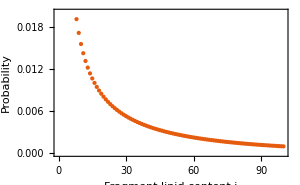

```mathematica
(* ldep fragment distribution *)
```

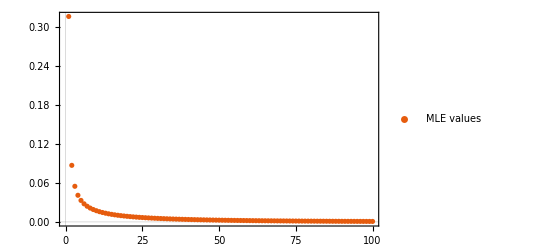

```mathematica
ListPlot[Table[{i,negbinom[i,18,1.8]},{i,1,100}],PlotTheme->"Scientific",Joined->False,PlotRange->All,PlotLegends->{"MLE values"}]
```